```mathematica
<<xAct`xTensor`
<<xAct`Invar`
<<xAct`xTras`
<<xAct`TexAct`
<<VariationalMethods`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.5, {2021,9,14}

CopyRight (C) 2011-2021, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.3, {2021,10,28}

CopyRight (C) 2008-2021, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

## 2

```mathematica
DefManifold[M4,4,IndexRange[a,n]]
DefMetric[-1,gmetric[-a,-b],CD,SymbolOfCovD->{";","∇"},PrintAs->"g"]
```

** DefManifold: Defining manifold M4.

** DefVBundle: Defining vbundle TangentM4.

** DefTensor: Defining symmetric metric tensor gmetric[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilongmetric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetragmetric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetragmetric†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Schouten tensor SchoutenCD[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCD[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCD[LI[_],-a,-b].

** DefTensor: Defining weight +2 density Detgmetric[]. Determinant.

** DefParameter: Defining parameter PerturbationParametergmetric.

** DefTensor: Defining tensor Perturbationgmetric[LI[order],-a,-b].

```mathematica
DefTensor[#,M4]&/@{ϕ[],A[-a],F[-a,-b]};
```

** DefTensor: Defining tensor ϕ[].

** DefTensor: Defining tensor A[-a].

** DefTensor: Defining tensor F[-a,-b].

```mathematica
IndexSet[F[-a_,-b_],CD[-a]@A[-b]-CD[-b]@A[-a]]
IndexSet[F[a_,b_],gmetric[a,c]*gmetric[b,d]*F[-c,-d]]
```

∇_a A |  
b-∇_b A |  
a

g | a | c
  |   g | b | d
  |   (∇_c A |  
d-∇_d A |  
c)

```mathematica
DefScalarFunction[#]&/@{V,func};
```

** DefScalarFunction: Defining scalar function V.

** DefScalarFunction: Defining scalar function func.

```mathematica
DefChart[chart4,M4,{0,1,2,3},{t[],x[],y[],z[]}]
```

** DefChart: Defining chart chart4.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar x[].

** DefTensor: Defining coordinate scalar y[].

** DefTensor: Defining coordinate scalar z[].

** DefMapping: Defining mapping chart4.

** DefMapping: Defining inverse mapping ichart4.

** DefTensor: Defining mapping differential tensor dichart4[-a,ichart4a].

** DefTensor: Defining mapping differential tensor dchart4[-a,chart4a].

** DefBasis: Defining basis chart4. Coordinated basis.

** DefCovD: Defining parallel derivative PDchart4[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDchart4[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDchart4[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDchart4[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDchart4[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpchart4[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownchart4[-a,-b,-c,-d].

```mathematica
DefScalarFunction[#]&/@{α,σ};
gmatrix={{-1, 0, 0, 0}, {0,ⅇ^(2*α[t[]])*ⅇ^(-4*σ[t[]]), 0, 0},{0, 0,ⅇ^(2*α[t[]])*ⅇ^(2*σ[t[]]), 0},{0, 0, 0,ⅇ^(2*α[t[]])*ⅇ^(2*σ[t[]])}};
MetricInBasis[gmetric,-chart4,gmatrix]
MetricInBasis[gmetric,chart4,Inverse[gmatrix]]
MetricCompute[gmetric,chart4,All,CVSimplify->Simplify,Parallelize->True]
```

** DefScalarFunction: Defining scalar function α.

** DefScalarFunction: Defining scalar function σ.

Added independent rule g |   |  
0 | 0→-1 for tensor gmetric

Added independent rule g |   |  
0 | 1→0 for tensor gmetric

Added independent rule g |   |  
0 | 2→0 for tensor gmetric

Added independent rule g |   |  
0 | 3→0 for tensor gmetric

Added dependent rule g |   |  
1 | 0→g |   |  
0 | 1 for tensor gmetric

Added independent rule g |   |  
1 | 1→ⅇ^(2 α[t]-4 σ[t]) for tensor gmetric

Added independent rule g |   |  
1 | 2→0 for tensor gmetric

Added independent rule g |   |  
1 | 3→0 for tensor gmetric

Added dependent rule g |   |  
2 | 0→g |   |  
0 | 2 for tensor gmetric

Added dependent rule g |   |  
2 | 1→g |   |  
1 | 2 for tensor gmetric

Added independent rule g |   |  
2 | 2→ⅇ^(2 (α[t]+σ[t])) for tensor gmetric

Added independent rule g |   |  
2 | 3→0 for tensor gmetric

Added dependent rule g |   |  
3 | 0→g |   |  
0 | 3 for tensor gmetric

Added dependent rule g |   |  
3 | 1→g |   |  
1 | 3 for tensor gmetric

Added dependent rule g |   |  
3 | 2→g |   |  
2 | 3 for tensor gmetric

Added independent rule g |   |  
3 | 3→ⅇ^(2 (α[t]+σ[t])) for tensor gmetric

{{g |   |  
0 | 0→-1,g |   |  
0 | 1→0,g |   |  
0 | 2→0,g |   |  
0 | 3→0},{g |   |  
1 | 0→0,g |   |  
1 | 1→ⅇ^(2 α[t]-4 σ[t]),g |   |  
1 | 2→0,g |   |  
1 | 3→0},{g |   |  
2 | 0→0,g |   |  
2 | 1→0,g |   |  
2 | 2→ⅇ^(2 (α[t]+σ[t])),g |   |  
2 | 3→0},{g |   |  
3 | 0→0,g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→ⅇ^(2 (α[t]+σ[t]))}}

Added independent rule g | 0 | 0
  |  →-1 for tensor gmetric

Added independent rule g | 0 | 1
  |  →0 for tensor gmetric

Added independent rule g | 0 | 2
  |  →0 for tensor gmetric

Added independent rule g | 0 | 3
  |  →0 for tensor gmetric

Added dependent rule g | 1 | 0
  |  →g | 0 | 1
  |   for tensor gmetric

Added independent rule g | 1 | 1
  |  →ⅇ^(-2 α[t]+4 σ[t]) for tensor gmetric

Added independent rule g | 1 | 2
  |  →0 for tensor gmetric

Added independent rule g | 1 | 3
  |  →0 for tensor gmetric

Added dependent rule g | 2 | 0
  |  →g | 0 | 2
  |   for tensor gmetric

Added dependent rule g | 2 | 1
  |  →g | 1 | 2
  |   for tensor gmetric

Added independent rule g | 2 | 2
  |  →ⅇ^(-2 (α[t]+σ[t])) for tensor gmetric

Added independent rule g | 2 | 3
  |  →0 for tensor gmetric

Added dependent rule g | 3 | 0
  |  →g | 0 | 3
  |   for tensor gmetric

Added dependent rule g | 3 | 1
  |  →g | 1 | 3
  |   for tensor gmetric

Added dependent rule g | 3 | 2
  |  →g | 2 | 3
  |   for tensor gmetric

Added independent rule g | 3 | 3
  |  →ⅇ^(-2 (α[t]+σ[t])) for tensor gmetric

{{g | 0 | 0
  |  →-1,g | 0 | 1
  |  →0,g | 0 | 2
  |  →0,g | 0 | 3
  |  →0},{g | 1 | 0
  |  →0,g | 1 | 1
  |  →ⅇ^(-2 α[t]+4 σ[t]),g | 1 | 2
  |  →0,g | 1 | 3
  |  →0},{g | 2 | 0
  |  →0,g | 2 | 1
  |  →0,g | 2 | 2
  |  →ⅇ^(-2 (α[t]+σ[t])),g | 2 | 3
  |  →0},{g | 3 | 0
  |  →0,g | 3 | 1
  |  →0,g | 3 | 2
  |  →0,g | 3 | 3
  |  →ⅇ^(-2 (α[t]+σ[t]))}}

** DefTensor: Defining weight +2 density Detgmetricchart4[]. Determinant.

** DefTensor: Defining tensor ChristoffelCDPDchart4[a,-b,-c].

```mathematica
DefScalarFunction[#]&/@{Ax,φ};
```

** DefScalarFunction: Defining scalar function Ax.

** DefScalarFunction: Defining scalar function φ.

```mathematica
DefConstantSymbol[κ];
```

** DefConstantSymbol: Defining constant symbol κ.

```mathematica
ComponentValue[ComponentArray[A[-{a,chart4}]],{0,Ax[t[]],0,0}]
ComponentValue[ComponentArray[A[{a,chart4}]],gmetric[{a,chart4},{b,chart4}]*A[-{b,chart4}]//TraceBasisDummy//ComponentArray//ToValues]
ComponentValue[ϕ[],φ[t[]]]
```

Added independent rule A |  
0→0 for tensor A

Added independent rule A |  
1→Ax[t] for tensor A

Added independent rule A |  
2→0 for tensor A

Added independent rule A |  
3→0 for tensor A

{A |  
0→0,A |  
1→Ax[t],A |  
2→0,A |  
3→0}

Added independent rule A | 0
 →0 for tensor A

Added independent rule A | 1
 →ⅇ^(-2 α[t]+4 σ[t]) Ax[t] for tensor A

Added independent rule A | 2
 →0 for tensor A

Added independent rule A | 3
 →0 for tensor A

{A | 0
 →0,A | 1
 →ⅇ^(-2 α[t]+4 σ[t]) Ax[t],A | 2
 →0,A | 3
 →0}

Added independent rule ϕ→φ[t] for tensor ϕ

ϕ→φ[t]

```mathematica
changeIndex=Table[Union[IndexRange[a,n],{n1,n10,n11,n12,n13,n14}][[temp]]->{Union[IndexRange[a,n],{n1,n10,n11,n12,n13,n14}][[temp]],chart4},{temp,1,Length[Union[IndexRange[a,n],{n1,n10,n11,n12,n13,n14}]]}];
```

```mathematica
RicciScalarCD[]/(2*κ^2)-1/2*CD[-a]@ϕ[]*CD[a]@ϕ[]-V[ϕ[]]-1/4*func[ϕ[]]^2*F[-a,-b]*F[a,b]
```

R[∇]/(2 κ^2)-V[ϕ]-1/2 ∇_a ϕ ∇^a ϕ-1/4 func[ϕ]^2 g | a | c
  |   g | b | d
  |   (∇_a A |  
b-∇_b A |  
a) (∇_c A |  
d-∇_d A |  
c)

```mathematica
R[∇]/(2 κ^2)-V[ϕ]-1/2 ∇_a ϕ ∇^a ϕ-1/4 func[ϕ]^2 {{g, {{a, c}, {, }}}} {{g, {{b, d}, {, }}}} (∇_a {{A, {{}, {b}}}}-∇_b {{A, {{}, {a}}}}) (∇_c {{A, {{}, {d}}}}-∇_d {{A, {{}, {c}}}})//ChangeCovD[#,CD,PD]&
```

R[∇]/(2 κ^2)-V[ϕ]-1/2 ∂_a ϕ ∂^a ϕ-1/4 func[ϕ]^2 g | a | c
  |   g | b | d
  |   (-A |  
e Γ[∇] | e |   |  
  | a | b+A |  
f Γ[∇] | f |   |  
  | b | a+∂_a A |  
b-∂_b A |  
a) (-A |  
g Γ[∇] | g |   |  
  | c | d+A |  
h Γ[∇] | h |   |  
  | d | c+∂_c A |  
d-∂_d A |  
c)

```mathematica
R[∇]/(2 κ^2)-V[ϕ]-1/2 D[ϕ, a] ∂^a ϕ-1/4 func[ϕ]^2 {{g, {{a, c}, {, }}}} {{g, {{b, d}, {, }}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, a, b}}}}+{{A, {{}, {f}}}} {{Γ[∇], {{f, , }, {, b, a}}}}+D[{{A, {{}, {b}}}}, a]-D[{{A, {{}, {a}}}}, b]) (-{{A, {{}, {g}}}} {{Γ[∇], {{g, , }, {, c, d}}}}+{{A, {{}, {h}}}} {{Γ[∇], {{h, , }, {, d, c}}}}+D[{{A, {{}, {d}}}}, c]-D[{{A, {{}, {c}}}}, d])/.changeIndex//TraceBasisDummy//ToValues//Simplify
```

1/(2 κ^2)ⅇ^(-4 (α[t]+σ[t])) (κ^2 Ax[t]^2 (ⅇ^(2 α[t]+8 σ[t]) (Γ[∇] | 1 |   |  
  | 0 | 1)^2+ⅇ^(2 (α[t]+σ[t])) (Γ[∇] | 1 |   |  
  | 0 | 2)^2+ⅇ^(2 (α[t]+σ[t])) (Γ[∇] | 1 |   |  
  | 0 | 3)^2-2 ⅇ^(2 α[t]+8 σ[t]) Γ[∇] | 1 |   |  
  | 0 | 1 Γ[∇] | 1 |   |  
  | 1 | 0+ⅇ^(2 α[t]+8 σ[t]) (Γ[∇] | 1 |   |  
  | 1 | 0)^2-ⅇ^(6 σ[t]) (Γ[∇] | 1 |   |  
  | 1 | 2)^2-ⅇ^(6 σ[t]) (Γ[∇] | 1 |   |  
  | 1 | 3)^2-2 ⅇ^(2 (α[t]+σ[t])) Γ[∇] | 1 |   |  
  | 0 | 2 Γ[∇] | 1 |   |  
  | 2 | 0+ⅇ^(2 (α[t]+σ[t])) (Γ[∇] | 1 |   |  
  | 2 | 0)^2+2 ⅇ^(6 σ[t]) Γ[∇] | 1 |   |  
  | 1 | 2 Γ[∇] | 1 |   |  
  | 2 | 1-ⅇ^(6 σ[t]) (Γ[∇] | 1 |   |  
  | 2 | 1)^2-(Γ[∇] | 1 |   |  
  | 2 | 3)^2-2 ⅇ^(2 (α[t]+σ[t])) Γ[∇] | 1 |   |  
  | 0 | 3 Γ[∇] | 1 |   |  
  | 3 | 0+ⅇ^(2 (α[t]+σ[t])) (Γ[∇] | 1 |   |  
  | 3 | 0)^2+2 ⅇ^(6 σ[t]) Γ[∇] | 1 |   |  
  | 1 | 3 Γ[∇] | 1 |   |  
  | 3 | 1-ⅇ^(6 σ[t]) (Γ[∇] | 1 |   |  
  | 3 | 1)^2+2 Γ[∇] | 1 |   |  
  | 2 | 3 Γ[∇] | 1 |   |  
  | 3 | 2-(Γ[∇] | 1 |   |  
  | 3 | 2)^2) func[φ[t]]^2-2 ⅇ^(2 α[t]+8 σ[t]) κ^2 Ax[t] (Γ[∇] | 1 |   |  
  | 0 | 1-Γ[∇] | 1 |   |  
  | 1 | 0) func[φ[t]]^2 Ax'[t]+ⅇ^(2 α[t]+4 σ[t]) (-2 ⅇ^(2 α[t]) κ^2 V[φ[t]]+ⅇ^(4 σ[t]) κ^2 func[φ[t]]^2 Ax'[t]^2+ⅇ^(2 α[t]) (12 α'[t]^2+6 σ'[t]^2-κ^2 g | 0 | 0
  |   φ'[t]^2+6 α''[t])))

```mathematica
ChristoffelCD[a,-b,-c]//ChristoffelToMetric
```

```mathematica
1/2 {{g, {{a, d}, {, }}}} (D[{{g, {{, }, {c, d}}}}, b]+D[{{g, {{, }, {b, d}}}}, c]-D[{{g, {{, }, {b, c}}}}, d])/.changeIndex
```

```mathematica
tempChristoffelCDComponentValue=1/2 {{g, {{a, d}, {, }}}} (D[{{g, {{, }, {c, d}}}}, b]+D[{{g, {{, }, {b, d}}}}, c]-D[{{g, {{, }, {b, c}}}}, d])//TraceBasisDummy//ComponentArray//ToValues// Flatten;
```

```mathematica
tempChristoffelCDComponent=ChristoffelCD[{a, chart4}, -{b, chart4}, -{c, chart4}] // ComponentArray // Flatten;
```

```mathematica
tempRule=Table[tempChristoffelCDComponent[[n]]->tempChristoffelCDComponentValue[[n]],{n,4^3}];
```

```mathematica
1/(2 κ^2)ⅇ^(-4 (α[t]+σ[t])) (κ^2 Ax[t]^2 (ⅇ^(2 α[t]+8 σ[t]) {{Γ[∇], {{1, , }, {, 0, 1}}}}^2+ⅇ^(2 (α[t]+σ[t])) {{Γ[∇], {{1, , }, {, 0, 2}}}}^2+ⅇ^(2 (α[t]+σ[t])) {{Γ[∇], {{1, , }, {, 0, 3}}}}^2-2 ⅇ^(2 α[t]+8 σ[t]) {{Γ[∇], {{1, , }, {, 0, 1}}}} {{Γ[∇], {{1, , }, {, 1, 0}}}}+ⅇ^(2 α[t]+8 σ[t]) {{Γ[∇], {{1, , }, {, 1, 0}}}}^2-ⅇ^(6 σ[t]) {{Γ[∇], {{1, , }, {, 1, 2}}}}^2-ⅇ^(6 σ[t]) {{Γ[∇], {{1, , }, {, 1, 3}}}}^2-2 ⅇ^(2 (α[t]+σ[t])) {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 2, 0}}}}+ⅇ^(2 (α[t]+σ[t])) {{Γ[∇], {{1, , }, {, 2, 0}}}}^2+2 ⅇ^(6 σ[t]) {{Γ[∇], {{1, , }, {, 1, 2}}}} {{Γ[∇], {{1, , }, {, 2, 1}}}}-ⅇ^(6 σ[t]) {{Γ[∇], {{1, , }, {, 2, 1}}}}^2-{{Γ[∇], {{1, , }, {, 2, 3}}}}^2-2 ⅇ^(2 (α[t]+σ[t])) {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 3, 0}}}}+ⅇ^(2 (α[t]+σ[t])) {{Γ[∇], {{1, , }, {, 3, 0}}}}^2+2 ⅇ^(6 σ[t]) {{Γ[∇], {{1, , }, {, 1, 3}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}}-ⅇ^(6 σ[t]) {{Γ[∇], {{1, , }, {, 3, 1}}}}^2+2 {{Γ[∇], {{1, , }, {, 2, 3}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}}-{{Γ[∇], {{1, , }, {, 3, 2}}}}^2) func[φ[t]]^2-2 ⅇ^(2 α[t]+8 σ[t]) κ^2 Ax[t] ({{Γ[∇], {{1, , }, {, 0, 1}}}}-{{Γ[∇], {{1, , }, {, 1, 0}}}}) func[φ[t]]^2 Ax'[t]+ⅇ^(2 α[t]+4 σ[t]) (-2 ⅇ^(2 α[t]) κ^2 V[φ[t]]+ⅇ^(4 σ[t]) κ^2 func[φ[t]]^2 Ax'[t]^2+ⅇ^(2 α[t]) (12 α'[t]^2+6 σ'[t]^2-κ^2 {{g, {{0, 0}, {, }}}} φ'[t]^2+6 α''[t])))/.tempRule//ToValues
```

1/(2 κ^2)ⅇ^(-4 (α[t]+σ[t])) (-2 ⅇ^(2 α[t]+8 σ[t]) κ^2 Ax[t] func[φ[t]]^2 Ax'[t] (1/2 (2 α'[t]-4 σ'[t])+1/2 (-2 α'[t]+4 σ'[t]))+ⅇ^(2 α[t]+4 σ[t]) (-2 ⅇ^(2 α[t]) κ^2 V[φ[t]]+ⅇ^(4 σ[t]) κ^2 func[φ[t]]^2 Ax'[t]^2+ⅇ^(2 α[t]) (12 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2+6 α''[t])))

对度规变分

```mathematica
(R[∇]/(2 κ^2)-V[ϕ]-1/2 ∇_a ϕ ∇^a ϕ-1/4 func[ϕ]^2 {{g, {{a, c}, {, }}}} {{g, {{b, d}, {, }}}} (∇_a {{A, {{}, {b}}}}-∇_b {{A, {{}, {a}}}}) (∇_c {{A, {{}, {d}}}}-∇_d {{A, {{}, {c}}}}))//ContractMetric//Simplify
```

1/4 ((2 R[∇])/κ^2-4 V[ϕ]-2 ∇_a ϕ ∇^a ϕ+func[ϕ]^2 (∇_b A | c
  (-∇^b A |  
c+∇_c A | b
 )+∇_a A | d
  (-∇^a A |  
d+∇_d A | a
 )))

```mathematica
VarL[gmetric[a,b]]@(1/4 ((2 R[∇])/κ^2-4 V[ϕ]-2 ∇_a ϕ ∇^a ϕ+func[ϕ]^2 (∇_b {{A, {{c}, {}}}} (-∇^b {{A, {{}, {c}}}}+∇_c {{A, {{b}, {}}}})+∇_a {{A, {{d}, {}}}} (-∇^a {{A, {{}, {d}}}}+∇_d {{A, {{a}, {}}}}))))//SeparateMetric[]//ChangeCovD[#,CD,PD]&
```

```mathematica
{{R[∇], {{, }, {a, b}}}}/(2 κ^2)-1/4 func[ϕ]^2 {{g, {{c, d}, {, }}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, a, d}}}}+D[{{A, {{}, {d}}}}, a]) (-{{A, {{}, {f}}}} {{Γ[∇], {{f, , }, {, b, c}}}}+D[{{A, {{}, {c}}}}, b])-1/4 func[ϕ]^2 {{g, {{c, d}, {, }}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, a, c}}}}+D[{{A, {{}, {c}}}}, a]) (-{{A, {{}, {f}}}} {{Γ[∇], {{f, , }, {, b, d}}}}+D[{{A, {{}, {d}}}}, b])-1/2 D[ϕ, a] D[ϕ, b]+1/2 func[ϕ]^2 {{g, {{c, d}, {, }}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, b, d}}}}+D[{{A, {{}, {d}}}}, b]) (-{{A, {{}, {f}}}} {{Γ[∇], {{f, , }, {, c, a}}}}+D[{{A, {{}, {a}}}}, c])+1/2 func[ϕ]^2 {{g, {{c, d}, {, }}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, a, d}}}}+D[{{A, {{}, {d}}}}, a]) (-{{A, {{}, {f}}}} {{Γ[∇], {{f, , }, {, c, b}}}}+D[{{A, {{}, {b}}}}, c])-1/4 func[ϕ]^2 {{g, {{c, d}, {, }}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, c, b}}}}+D[{{A, {{}, {b}}}}, c]) (-{{A, {{}, {f}}}} {{Γ[∇], {{f, , }, {, d, a}}}}+D[{{A, {{}, {a}}}}, d])-1/4 func[ϕ]^2 {{g, {{c, d}, {, }}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, c, a}}}}+D[{{A, {{}, {a}}}}, c]) (-{{A, {{}, {f}}}} {{Γ[∇], {{f, , }, {, d, b}}}}+D[{{A, {{}, {b}}}}, d])+1/8 {{A, {{}, {b}}}} func[ϕ]^2 {{g, {{c, d}, {, }}}} (-{{Γ[∇], {{g, , }, {, d, c}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, a, g}}}}+D[{{A, {{}, {g}}}}, a])-{{Γ[∇], {{e, , }, {, a, c}}}} D[{{A, {{}, {e}}}}, d]-{{A, {{}, {e}}}} D[{{Γ[∇], {{e, , }, {, a, c}}}}, d]+∂_d ∂_a {{A, {{}, {c}}}}-{{Γ[∇], {{f, , }, {, d, a}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, f, c}}}}+D[{{A, {{}, {c}}}}, f]))+1/8 {{A, {{}, {a}}}} func[ϕ]^2 {{g, {{c, d}, {, }}}} (-{{Γ[∇], {{g, , }, {, d, c}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, b, g}}}}+D[{{A, {{}, {g}}}}, b])-{{Γ[∇], {{e, , }, {, b, c}}}} D[{{A, {{}, {e}}}}, d]-{{A, {{}, {e}}}} D[{{Γ[∇], {{e, , }, {, b, c}}}}, d]+∂_d ∂_b {{A, {{}, {c}}}}-{{Γ[∇], {{f, , }, {, d, b}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, f, c}}}}+D[{{A, {{}, {c}}}}, f]))-1/8 {{A, {{}, {b}}}} func[ϕ]^2 {{g, {{c, d}, {, }}}} (-{{Γ[∇], {{g, , }, {, c, d}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, a, g}}}}+D[{{A, {{}, {g}}}}, a])-{{Γ[∇], {{e, , }, {, a, d}}}} D[{{A, {{}, {e}}}}, c]-{{A, {{}, {e}}}} D[{{Γ[∇], {{e, , }, {, a, d}}}}, c]+∂_c ∂_a {{A, {{}, {d}}}}-{{Γ[∇], {{f, , }, {, c, a}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, f, d}}}}+D[{{A, {{}, {d}}}}, f]))-1/8 {{A, {{}, {a}}}} func[ϕ]^2 {{g, {{c, d}, {, }}}} (-{{Γ[∇], {{g, , }, {, c, d}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, b, g}}}}+D[{{A, {{}, {g}}}}, b])-{{Γ[∇], {{e, , }, {, b, d}}}} D[{{A, {{}, {e}}}}, c]-{{A, {{}, {e}}}} D[{{Γ[∇], {{e, , }, {, b, d}}}}, c]+∂_c ∂_b {{A, {{}, {d}}}}-{{Γ[∇], {{f, , }, {, c, b}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, f, d}}}}+D[{{A, {{}, {d}}}}, f]))+1/8 {{A, {{}, {b}}}} func[ϕ]^2 {{g, {{c, d}, {, }}}} (-{{Γ[∇], {{e, , }, {, d, a}}}} D[{{A, {{}, {e}}}}, c]-{{A, {{}, {e}}}} D[{{Γ[∇], {{e, , }, {, d, a}}}}, c]+∂_c ∂_d {{A, {{}, {a}}}}-{{Γ[∇], {{f, , }, {, c, a}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, d, f}}}}+D[{{A, {{}, {f}}}}, d])-{{Γ[∇], {{g, , }, {, c, d}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, g, a}}}}+D[{{A, {{}, {a}}}}, g]))-1/8 {{A, {{}, {b}}}} func[ϕ]^2 {{g, {{c, d}, {, }}}} (-{{Γ[∇], {{f, , }, {, d, a}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, c, f}}}}+D[{{A, {{}, {f}}}}, c])-{{Γ[∇], {{e, , }, {, c, a}}}} D[{{A, {{}, {e}}}}, d]-{{A, {{}, {e}}}} D[{{Γ[∇], {{e, , }, {, c, a}}}}, d]+∂_d ∂_c {{A, {{}, {a}}}}-{{Γ[∇], {{g, , }, {, d, c}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, g, a}}}}+D[{{A, {{}, {a}}}}, g]))+1/8 {{A, {{}, {a}}}} func[ϕ]^2 {{g, {{c, d}, {, }}}} (-{{Γ[∇], {{e, , }, {, d, b}}}} D[{{A, {{}, {e}}}}, c]-{{A, {{}, {e}}}} D[{{Γ[∇], {{e, , }, {, d, b}}}}, c]+∂_c ∂_d {{A, {{}, {b}}}}-{{Γ[∇], {{f, , }, {, c, b}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, d, f}}}}+D[{{A, {{}, {f}}}}, d])-{{Γ[∇], {{g, , }, {, c, d}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, g, b}}}}+D[{{A, {{}, {b}}}}, g]))-1/8 {{A, {{}, {a}}}} func[ϕ]^2 {{g, {{c, d}, {, }}}} (-{{Γ[∇], {{f, , }, {, d, b}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, c, f}}}}+D[{{A, {{}, {f}}}}, c])-{{Γ[∇], {{e, , }, {, c, b}}}} D[{{A, {{}, {e}}}}, d]-{{A, {{}, {e}}}} D[{{Γ[∇], {{e, , }, {, c, b}}}}, d]+∂_d ∂_c {{A, {{}, {b}}}}-{{Γ[∇], {{g, , }, {, d, c}}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, g, b}}}}+D[{{A, {{}, {b}}}}, g]))-1/8 {{g, {{, }, {a, b}}}} ((2 R[∇])/κ^2-4 V[ϕ]-2 {{g, {{c, g}, {, }}}} D[ϕ, c] D[ϕ, g]+func[ϕ]^2 ({{g, {{e, h}, {, }}}} (-{{A, {{}, {n}}}} {{Γ[∇], {{n, , }, {, d, h}}}}+D[{{A, {{}, {h}}}}, d]) ({{g, {{d, j}, {, }}}} (-{{A, {{}, {n1}}}} {{Γ[∇], {{n1, , }, {, e, j}}}}+D[{{A, {{}, {j}}}}, e])-{{g, {{d, i}, {, }}}} (-{{A, {{}, {n10}}}} {{Γ[∇], {{n10, , }, {, i, e}}}}+D[{{A, {{}, {e}}}}, i]))+{{g, {{f, k}, {, }}}} (-{{A, {{}, {n11}}}} {{Γ[∇], {{n11, , }, {, c, k}}}}+D[{{A, {{}, {k}}}}, c]) ({{g, {{c, m}, {, }}}} (-{{A, {{}, {n12}}}} {{Γ[∇], {{n12, , }, {, f, m}}}}+D[{{A, {{}, {m}}}}, f])-{{g, {{c, l}, {, }}}} (-{{A, {{}, {n13}}}} {{Γ[∇], {{n13, , }, {, l, f}}}}+D[{{A, {{}, {f}}}}, l]))))-1/4 {{A, {{}, {b}}}} func[ϕ] {{g, {{c, d}, {, }}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, a, d}}}}+D[{{A, {{}, {d}}}}, a]) D[ϕ, c] func'[ϕ]-1/4 {{A, {{}, {a}}}} func[ϕ] {{g, {{c, d}, {, }}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, b, d}}}}+D[{{A, {{}, {d}}}}, b]) D[ϕ, c] func'[ϕ]+1/4 {{A, {{}, {b}}}} func[ϕ] {{g, {{c, d}, {, }}}} D[ϕ, c] (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, d, a}}}}+D[{{A, {{}, {a}}}}, d]) func'[ϕ]+1/4 {{A, {{}, {a}}}} func[ϕ] {{g, {{c, d}, {, }}}} D[ϕ, c] (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, d, b}}}}+D[{{A, {{}, {b}}}}, d]) func'[ϕ]+1/4 {{A, {{}, {b}}}} func[ϕ] {{g, {{c, d}, {, }}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, a, c}}}}+D[{{A, {{}, {c}}}}, a]) D[ϕ, d] func'[ϕ]+1/4 {{A, {{}, {a}}}} func[ϕ] {{g, {{c, d}, {, }}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, b, c}}}}+D[{{A, {{}, {c}}}}, b]) D[ϕ, d] func'[ϕ]-1/4 {{A, {{}, {b}}}} func[ϕ] {{g, {{c, d}, {, }}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, c, a}}}}+D[{{A, {{}, {a}}}}, c]) D[ϕ, d] func'[ϕ]-1/4 {{A, {{}, {a}}}} func[ϕ] {{g, {{c, d}, {, }}}} (-{{A, {{}, {e}}}} {{Γ[∇], {{e, , }, {, c, b}}}}+D[{{A, {{}, {b}}}}, c]) D[ϕ, d] func'[ϕ]/.changeIndex//TraceBasisDummy//ComponentArray//ToValues
```

```mathematica
{{-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}}^2 func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}}^2 func[φ[t]]^2-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 0}}}}^2 func[φ[t]]^2+ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 2, 0}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 0}}}}^2 func[φ[t]]^2+ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 3, 0}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 3, 0}}}}^2 func[φ[t]]^2-ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 0}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])-1/2 ⅇ^(-2 α[t]+4 σ[t]) func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])^2-1/2 φ'[t]^2-(3 (α'[t]^2+2 σ'[t]^2+α''[t]))/(2 κ^2)+1/8 (-4 V[φ[t]]+func[φ[t]]^2 (-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 2}}}} (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 2}}}}+Ax[t] {{Γ[∇], {{1, , }, {, 2, 0}}}})+2 Ax[t] {{Γ[∇], {{1, , }, {, 2, 0}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 2}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 0}}}})-2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 2, 1}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 2}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 2}}}} (ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 2}}}}-ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 2, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 3}}}} (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 3}}}}+Ax[t] {{Γ[∇], {{1, , }, {, 3, 0}}}})+2 Ax[t] {{Γ[∇], {{1, , }, {, 3, 0}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 3}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 0}}}})-2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 3, 1}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 3}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 3}}}} (ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 3}}}}-ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 3, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 3}}}} (ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 3}}}}-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 2}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 2}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 3}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 2}}}})+2 ⅇ^(-2 α[t]+4 σ[t]) (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t]) (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax[t] {{Γ[∇], {{1, , }, {, 1, 0}}}}+Ax'[t])+2 Ax[t] {{Γ[∇], {{1, , }, {, 1, 0}}}} (ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 0}}}}+ⅇ^(-2 α[t]+4 σ[t]) (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])))+2 φ'[t]^2+(12 (2 α'[t]^2+σ'[t]^2+α''[t]))/κ^2),-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 1, 2}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 1, 3}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 2}}}} {{Γ[∇], {{1, , }, {, 2, 0}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 2, 1}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 0}}}} {{Γ[∇], {{1, , }, {, 2, 1}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 3}}}} {{Γ[∇], {{1, , }, {, 3, 0}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 3, 0}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2,-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 0}}}} {{Γ[∇], {{1, , }, {, 1, 2}}}} func[φ[t]]^2+1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 0}}}} {{Γ[∇], {{1, , }, {, 2, 1}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 2, 3}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 3}}}} {{Γ[∇], {{1, , }, {, 3, 0}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 3, 0}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 2}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])+1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 2, 1}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t]),-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 0}}}} {{Γ[∇], {{1, , }, {, 1, 3}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 2, 3}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 0}}}} {{Γ[∇], {{1, , }, {, 2, 3}}}} func[φ[t]]^2+1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 0}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 0}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 3}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])+1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])},{-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 1, 2}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 1, 3}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 2}}}} {{Γ[∇], {{1, , }, {, 2, 0}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 2, 1}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 0}}}} {{Γ[∇], {{1, , }, {, 2, 1}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 3}}}} {{Γ[∇], {{1, , }, {, 3, 0}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 3, 0}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2,1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 0}}}}^2 func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 2}}}}^2 func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 3}}}}^2 func[φ[t]]^2+ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 2}}}} {{Γ[∇], {{1, , }, {, 2, 1}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 1}}}}^2 func[φ[t]]^2+ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 3}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 3, 1}}}}^2 func[φ[t]]^2+Ax[t] {{Γ[∇], {{1, , }, {, 1, 0}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])+1/2 func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])^2-1/8 ⅇ^(2 α[t]-4 σ[t]) (-4 V[φ[t]]+func[φ[t]]^2 (-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 2}}}} (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 2}}}}+Ax[t] {{Γ[∇], {{1, , }, {, 2, 0}}}})+2 Ax[t] {{Γ[∇], {{1, , }, {, 2, 0}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 2}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 0}}}})-2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 2, 1}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 2}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 2}}}} (ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 2}}}}-ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 2, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 3}}}} (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 3}}}}+Ax[t] {{Γ[∇], {{1, , }, {, 3, 0}}}})+2 Ax[t] {{Γ[∇], {{1, , }, {, 3, 0}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 3}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 0}}}})-2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 3, 1}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 3}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 3}}}} (ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 3}}}}-ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 3, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 3}}}} (ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 3}}}}-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 2}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 2}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 3}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 2}}}})+2 ⅇ^(-2 α[t]+4 σ[t]) (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t]) (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax[t] {{Γ[∇], {{1, , }, {, 1, 0}}}}+Ax'[t])+2 Ax[t] {{Γ[∇], {{1, , }, {, 1, 0}}}} (ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 0}}}}+ⅇ^(-2 α[t]+4 σ[t]) (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])))+2 φ'[t]^2+(12 (2 α'[t]^2+σ'[t]^2+α''[t]))/κ^2)+(ⅇ^(2 α[t]-4 σ[t]) (3 α'[t]^2-6 α'[t] σ'[t]+α''[t]-2 σ''[t]))/(2 κ^2),-1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 1, 0}}}} func[φ[t]]^2+1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 0}}}} {{Γ[∇], {{1, , }, {, 2, 0}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 3}}}} {{Γ[∇], {{1, , }, {, 2, 3}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 3}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 3}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 3, 1}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2-1/2 Ax[t] {{Γ[∇], {{1, , }, {, 0, 2}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])+1/2 Ax[t] {{Γ[∇], {{1, , }, {, 2, 0}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t]),-1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 1, 0}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 2}}}} {{Γ[∇], {{1, , }, {, 2, 3}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 1}}}} {{Γ[∇], {{1, , }, {, 2, 3}}}} func[φ[t]]^2+1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 0}}}} {{Γ[∇], {{1, , }, {, 3, 0}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 2}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 1}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2-1/2 Ax[t] {{Γ[∇], {{1, , }, {, 0, 3}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])+1/2 Ax[t] {{Γ[∇], {{1, , }, {, 3, 0}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])},{-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 0}}}} {{Γ[∇], {{1, , }, {, 1, 2}}}} func[φ[t]]^2+1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 0}}}} {{Γ[∇], {{1, , }, {, 2, 1}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 2, 3}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 3}}}} {{Γ[∇], {{1, , }, {, 3, 0}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 3, 0}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 2}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])+1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 2, 1}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t]),-1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 1, 0}}}} func[φ[t]]^2+1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 0}}}} {{Γ[∇], {{1, , }, {, 2, 0}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 3}}}} {{Γ[∇], {{1, , }, {, 2, 3}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 3}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 3}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 3, 1}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2-1/2 Ax[t] {{Γ[∇], {{1, , }, {, 0, 2}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])+1/2 Ax[t] {{Γ[∇], {{1, , }, {, 2, 0}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t]),1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}}^2 func[φ[t]]^2-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 2}}}}^2 func[φ[t]]^2-Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 2, 0}}}} func[φ[t]]^2+1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 0}}}}^2 func[φ[t]]^2+ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 2}}}} {{Γ[∇], {{1, , }, {, 2, 1}}}} func[φ[t]]^2-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 1}}}}^2 func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 3}}}}^2 func[φ[t]]^2+ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 3}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 3, 2}}}}^2 func[φ[t]]^2-1/8 ⅇ^(2 (α[t]+σ[t])) (-4 V[φ[t]]+func[φ[t]]^2 (-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 2}}}} (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 2}}}}+Ax[t] {{Γ[∇], {{1, , }, {, 2, 0}}}})+2 Ax[t] {{Γ[∇], {{1, , }, {, 2, 0}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 2}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 0}}}})-2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 2, 1}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 2}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 2}}}} (ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 2}}}}-ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 2, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 3}}}} (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 3}}}}+Ax[t] {{Γ[∇], {{1, , }, {, 3, 0}}}})+2 Ax[t] {{Γ[∇], {{1, , }, {, 3, 0}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 3}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 0}}}})-2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 3, 1}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 3}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 3}}}} (ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 3}}}}-ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 3, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 3}}}} (ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 3}}}}-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 2}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 2}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 3}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 2}}}})+2 ⅇ^(-2 α[t]+4 σ[t]) (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t]) (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax[t] {{Γ[∇], {{1, , }, {, 1, 0}}}}+Ax'[t])+2 Ax[t] {{Γ[∇], {{1, , }, {, 1, 0}}}} (ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 0}}}}+ⅇ^(-2 α[t]+4 σ[t]) (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])))+2 φ'[t]^2+(12 (2 α'[t]^2+σ'[t]^2+α''[t]))/κ^2)+(ⅇ^(2 (α[t]+σ[t])) (3 α'[t]^2+3 α'[t] σ'[t]+α''[t]+σ''[t]))/(2 κ^2),1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 0, 3}}}} func[φ[t]]^2-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 2}}}} {{Γ[∇], {{1, , }, {, 1, 3}}}} func[φ[t]]^2-1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 2, 0}}}} func[φ[t]]^2+1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 3}}}} {{Γ[∇], {{1, , }, {, 2, 1}}}} func[φ[t]]^2-1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 3, 0}}}} func[φ[t]]^2+1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 0}}}} {{Γ[∇], {{1, , }, {, 3, 0}}}} func[φ[t]]^2+1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 2}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 1}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2},{-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 0}}}} {{Γ[∇], {{1, , }, {, 1, 3}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 2, 3}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 0}}}} {{Γ[∇], {{1, , }, {, 2, 3}}}} func[φ[t]]^2+1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 0}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 0}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 3}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])+1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t]),-1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 1, 0}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 2}}}} {{Γ[∇], {{1, , }, {, 2, 3}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 1}}}} {{Γ[∇], {{1, , }, {, 2, 3}}}} func[φ[t]]^2+1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 0}}}} {{Γ[∇], {{1, , }, {, 3, 0}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 2}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2+1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 1}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2-1/2 Ax[t] {{Γ[∇], {{1, , }, {, 0, 3}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])+1/2 Ax[t] {{Γ[∇], {{1, , }, {, 3, 0}}}} func[φ[t]]^2 (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t]),1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 0, 3}}}} func[φ[t]]^2-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 2}}}} {{Γ[∇], {{1, , }, {, 1, 3}}}} func[φ[t]]^2-1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 2, 0}}}} func[φ[t]]^2+1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 3}}}} {{Γ[∇], {{1, , }, {, 2, 1}}}} func[φ[t]]^2-1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 2}}}} {{Γ[∇], {{1, , }, {, 3, 0}}}} func[φ[t]]^2+1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 0}}}} {{Γ[∇], {{1, , }, {, 3, 0}}}} func[φ[t]]^2+1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 2}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 1}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2,1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}}^2 func[φ[t]]^2-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 3}}}}^2 func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 3}}}}^2 func[φ[t]]^2-Ax[t]^2 {{Γ[∇], {{1, , }, {, 0, 3}}}} {{Γ[∇], {{1, , }, {, 3, 0}}}} func[φ[t]]^2+1/2 Ax[t]^2 {{Γ[∇], {{1, , }, {, 3, 0}}}}^2 func[φ[t]]^2+ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 1, 3}}}} {{Γ[∇], {{1, , }, {, 3, 1}}}} func[φ[t]]^2-1/2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t]^2 {{Γ[∇], {{1, , }, {, 3, 1}}}}^2 func[φ[t]]^2+ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 2, 3}}}} {{Γ[∇], {{1, , }, {, 3, 2}}}} func[φ[t]]^2-1/2 ⅇ^(-2 (α[t]+σ[t])) Ax[t]^2 {{Γ[∇], {{1, , }, {, 3, 2}}}}^2 func[φ[t]]^2-1/8 ⅇ^(2 (α[t]+σ[t])) (-4 V[φ[t]]+func[φ[t]]^2 (-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 2}}}} (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 2}}}}+Ax[t] {{Γ[∇], {{1, , }, {, 2, 0}}}})+2 Ax[t] {{Γ[∇], {{1, , }, {, 2, 0}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 2}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 0}}}})-2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 2, 1}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 2}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 2}}}} (ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 2}}}}-ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 2, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 3}}}} (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 3}}}}+Ax[t] {{Γ[∇], {{1, , }, {, 3, 0}}}})+2 Ax[t] {{Γ[∇], {{1, , }, {, 3, 0}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 0, 3}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 0}}}})-2 ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 3, 1}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 3}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 1, 3}}}} (ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 3}}}}-ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 3, 1}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 3}}}} (ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 3}}}}-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 2}}}})-2 ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 2}}}} (-ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 2, 3}}}}+ⅇ^(-2 (α[t]+σ[t])) Ax[t] {{Γ[∇], {{1, , }, {, 3, 2}}}})+2 ⅇ^(-2 α[t]+4 σ[t]) (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t]) (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax[t] {{Γ[∇], {{1, , }, {, 1, 0}}}}+Ax'[t])+2 Ax[t] {{Γ[∇], {{1, , }, {, 1, 0}}}} (ⅇ^(-2 α[t]+4 σ[t]) Ax[t] {{Γ[∇], {{1, , }, {, 1, 0}}}}+ⅇ^(-2 α[t]+4 σ[t]) (-Ax[t] {{Γ[∇], {{1, , }, {, 0, 1}}}}+Ax'[t])))+2 φ'[t]^2+(12 (2 α'[t]^2+σ'[t]^2+α''[t]))/κ^2)+(ⅇ^(2 (α[t]+σ[t])) (3 α'[t]^2+3 α'[t] σ'[t]+α''[t]+σ''[t]))/(2 κ^2)}}/.tempRule/.Ax'[t[]]->pA/(func[φ[t[]]]^2*ⅇ^(α[t[]]+4*σ[t[]]))//Simplify//MatrixForm
```

(1/4 (-(ⅇ^(-4 (α[t]+σ[t])) pA^2)/func[φ[t]]^2-2 V[φ[t]]+(6 α'[t]^2)/κ^2-(6 σ'[t]^2)/κ^2-φ'[t]^2) | 0 | 0 | 0
0 | (ⅇ^(-2 (α[t]+4 σ[t])) (pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (2 κ^2 V[φ[t]]-6 α'[t]^2-12 α'[t] σ'[t]-6 σ'[t]^2-κ^2 φ'[t]^2-4 α''[t]-4 σ''[t])))/(4 κ^2 func[φ[t]]^2) | 0 | 0
0 | 0 | -(ⅇ^(-2 (α[t]+σ[t])) pA^2)/(4 func[φ[t]]^2)+(ⅇ^(2 (α[t]+σ[t])) (2 κ^2 V[φ[t]]-6 α'[t]^2+6 α'[t] σ'[t]-6 σ'[t]^2-κ^2 φ'[t]^2-4 α''[t]+2 σ''[t]))/(4 κ^2) | 0
0 | 0 | 0 | -(ⅇ^(-2 (α[t]+σ[t])) pA^2)/(4 func[φ[t]]^2)+(ⅇ^(2 (α[t]+σ[t])) (2 κ^2 V[φ[t]]-6 α'[t]^2+6 α'[t] σ'[t]-6 σ'[t]^2-κ^2 φ'[t]^2-4 α''[t]+2 σ''[t]))/(4 κ^2))

```mathematica
{-(ⅇ^(-4 (α[t]+σ[t])) pA^2)/func[φ[t]]^2-2 V[φ[t]]+(6 α'[t]^2)/κ^2-(6 σ'[t]^2)/κ^2-φ'[t]^2==0,pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (2 κ^2 V[φ[t]]-6 α'[t]^2-12 α'[t] σ'[t]-6 σ'[t]^2-κ^2 φ'[t]^2-4 α''[t]-4 σ''[t])==0,-(ⅇ^(-2 (α[t]+σ[t])) pA^2)/(4 func[φ[t]]^2)+(ⅇ^(2 (α[t]+σ[t])) (2 κ^2 V[φ[t]]-6 α'[t]^2+6 α'[t] σ'[t]-6 σ'[t]^2-κ^2 φ'[t]^2-4 α''[t]+2 σ''[t]))/(4 κ^2)==0}
```

```mathematica
-(ⅇ^(-2 (α[t]+σ[t])) pA^2)/(4 func[φ[t]]^2)+(ⅇ^(2 (α[t]+σ[t])) (2 κ^2 V[φ[t]]-6 α'[t]^2+6 α'[t] σ'[t]-6 σ'[t]^2-κ^2 φ'[t]^2-4 α''[t]+2 σ''[t]))/(4 κ^2)//Together
```

1/(4 κ^2 func[φ[t]]^2)ⅇ^(-2 α[t]-2 σ[t]) (-pA^2 κ^2+2 ⅇ^(4 α[t]+4 σ[t]) κ^2 func[φ[t]]^2 V[φ[t]]-6 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 α'[t]^2+6 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 α'[t] σ'[t]-6 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 σ'[t]^2-ⅇ^(4 α[t]+4 σ[t]) κ^2 func[φ[t]]^2 φ'[t]^2-4 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 α''[t]+2 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 σ''[t])

```mathematica
-pA^2 κ^2+2 ⅇ^(4 α[t]+4 σ[t]) κ^2 func[φ[t]]^2 V[φ[t]]-6 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 α'[t]^2+6 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 α'[t] σ'[t]-6 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 σ'[t]^2-ⅇ^(4 α[t]+4 σ[t]) κ^2 func[φ[t]]^2 φ'[t]^2-4 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 α''[t]+2 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 σ''[t]//Simplify
```

```mathematica
(-pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (2 κ^2 V[φ[t]]-6 α'[t]^2+6 α'[t] σ'[t]-6 σ'[t]^2-κ^2 φ'[t]^2-4 α''[t]+2 σ''[t]))-(pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (2 κ^2 V[φ[t]]-6 α'[t]^2-12 α'[t] σ'[t]-6 σ'[t]^2-κ^2 φ'[t]^2-4 α''[t]-4 σ''[t]))//Simplify
```

-2 pA^2 κ^2+6 ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (3 α'[t] σ'[t]+σ''[t])

对 Ax[t[]] 变分

```mathematica
VariationalD[√(-Detgmetricchart4[]//ToValues)*1/(2 κ^2)ⅇ^(-4 (α[t]+σ[t])) (-2 ⅇ^(2 α[t]+8 σ[t]) κ^2 Ax[t] func[φ[t]]^2 Ax'[t] (1/2 (2 α'[t]-4 σ'[t])+1/2 (-2 α'[t]+4 σ'[t]))+ⅇ^(2 α[t]+4 σ[t]) (-2 ⅇ^(2 α[t]) κ^2 V[φ[t]]+ⅇ^(4 σ[t]) κ^2 func[φ[t]]^2 Ax'[t]^2+ⅇ^(2 α[t]) (12 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2+6 α''[t]))),Ax[t[]],t[]]//Simplify
```

-ⅇ^(-2 α[t]+4 σ[t]) √(ⅇ^(6 α[t])) func[φ[t]] (2 Ax'[t] func'[φ[t]] φ'[t]+func[φ[t]] (Ax'[t] (α'[t]+4 σ'[t])+Ax''[t]))

```mathematica
Ax'[t[]]->pA/(func[φ[t[]]]^2*ⅇ^(α[t[]]+4*σ[t[]]))
```

Ax'[t]→(ⅇ^(-α[t]-4 σ[t]) pA)/func[φ[t]]^2

```mathematica
VariationalD[√(-Detgmetricchart4[]//ToValues)*1/(2 κ^2)ⅇ^(-4 (α[t]+σ[t])) (-2 ⅇ^(2 α[t]+8 σ[t]) κ^2 Ax[t] func[φ[t]]^2 Ax'[t] (1/2 (2 α'[t]-4 σ'[t])+1/2 (-2 α'[t]+4 σ'[t]))+ⅇ^(2 α[t]+4 σ[t]) (-2 ⅇ^(2 α[t]) κ^2 V[φ[t]]+ⅇ^(4 σ[t]) κ^2 func[φ[t]]^2 Ax'[t]^2+ⅇ^(2 α[t]) (12 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2+6 α''[t]))),α[t[]],t[]]/.Ax'[t[]]->pA/(func[φ[t[]]]^2*ⅇ^(α[t[]]+4*σ[t[]]))//Simplify
VariationalD[√(-Detgmetricchart4[]//ToValues)*1/(2 κ^2)ⅇ^(-4 (α[t]+σ[t])) (-2 ⅇ^(2 α[t]+8 σ[t]) κ^2 Ax[t] func[φ[t]]^2 Ax'[t] (1/2 (2 α'[t]-4 σ'[t])+1/2 (-2 α'[t]+4 σ'[t]))+ⅇ^(2 α[t]+4 σ[t]) (-2 ⅇ^(2 α[t]) κ^2 V[φ[t]]+ⅇ^(4 σ[t]) κ^2 func[φ[t]]^2 Ax'[t]^2+ⅇ^(2 α[t]) (12 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2+6 α''[t]))),σ[t[]],t[]]/.Ax'[t[]]->pA/(func[φ[t[]]]^2*ⅇ^(α[t[]]+4*σ[t[]]))//Simplify
VariationalD[√(-Detgmetricchart4[]//ToValues)*1/(2 κ^2)ⅇ^(-4 (α[t]+σ[t])) (-2 ⅇ^(2 α[t]+8 σ[t]) κ^2 Ax[t] func[φ[t]]^2 Ax'[t] (1/2 (2 α'[t]-4 σ'[t])+1/2 (-2 α'[t]+4 σ'[t]))+ⅇ^(2 α[t]+4 σ[t]) (-2 ⅇ^(2 α[t]) κ^2 V[φ[t]]+ⅇ^(4 σ[t]) κ^2 func[φ[t]]^2 Ax'[t]^2+ⅇ^(2 α[t]) (12 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2+6 α''[t]))),φ[t[]],t[]]/.Ax'[t[]]->pA/(func[φ[t[]]]^2*ⅇ^(α[t[]]+4*σ[t[]]))//Simplify
```

1/2 √(ⅇ^(6 α[t])) ((ⅇ^(-4 (α[t]+σ[t])) pA^2)/func[φ[t]]^2+(3 (-2 κ^2 V[φ[t]]+6 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2+4 α''[t]))/κ^2)

2 √(ⅇ^(6 α[t])) ((ⅇ^(-4 (α[t]+σ[t])) pA^2)/func[φ[t]]^2-(3 (3 α'[t] σ'[t]+σ''[t]))/κ^2)

√(ⅇ^(6 α[t])) ((ⅇ^(-4 (α[t]+σ[t])) pA^2 func'[φ[t]])/func[φ[t]]^3-V'[φ[t]]-3 α'[t] φ'[t]-φ''[t])

```mathematica
(ⅇ^(-4 (α[t]+σ[t])) pA^2)/func[φ[t]]^2+(3 (-2 κ^2 V[φ[t]]+6 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2+4 α''[t]))/κ^2//Together
```

-1/(κ^2 func[φ[t]]^2)ⅇ^(-4 α[t]-4 σ[t]) (-pA^2 κ^2+6 ⅇ^(4 α[t]+4 σ[t]) κ^2 func[φ[t]]^2 V[φ[t]]-18 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 α'[t]^2-18 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 σ'[t]^2-3 ⅇ^(4 α[t]+4 σ[t]) κ^2 func[φ[t]]^2 φ'[t]^2-12 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 α''[t])

```mathematica
-pA^2 κ^2+6 ⅇ^(4 α[t]+4 σ[t]) κ^2 func[φ[t]]^2 V[φ[t]]-18 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 α'[t]^2-18 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 σ'[t]^2-3 ⅇ^(4 α[t]+4 σ[t]) κ^2 func[φ[t]]^2 φ'[t]^2-12 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 α''[t]//Simplify
```

-pA^2 κ^2+3 ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (2 κ^2 V[φ[t]]-6 α'[t]^2-6 σ'[t]^2-κ^2 φ'[t]^2-4 α''[t])

```mathematica
-(ⅇ^(-4 (α[t]+σ[t])) pA^2)/func[φ[t]]^2-2 V[φ[t]]+(6 α'[t]^2)/κ^2-(6 σ'[t]^2)/κ^2-φ'[t]^2//Together
```

-1/(κ^2 func[φ[t]]^2)ⅇ^(-4 α[t]-4 σ[t]) (pA^2 κ^2+2 ⅇ^(4 α[t]+4 σ[t]) κ^2 func[φ[t]]^2 V[φ[t]]-6 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 α'[t]^2+6 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 σ'[t]^2+ⅇ^(4 α[t]+4 σ[t]) κ^2 func[φ[t]]^2 φ'[t]^2)

```mathematica
pA^2 κ^2+2 ⅇ^(4 α[t]+4 σ[t]) κ^2 func[φ[t]]^2 V[φ[t]]-6 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 α'[t]^2+6 ⅇ^(4 α[t]+4 σ[t]) func[φ[t]]^2 σ'[t]^2+ⅇ^(4 α[t]+4 σ[t]) κ^2 func[φ[t]]^2 φ'[t]^2//Simplify
```

pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (2 κ^2 V[φ[t]]-6 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2)

```mathematica
3*(pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (2 κ^2 V[φ[t]]-6 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2))+(-pA^2 κ^2+3 ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (2 κ^2 V[φ[t]]-6 α'[t]^2-6 σ'[t]^2-κ^2 φ'[t]^2-4 α''[t]))//Simplify
```

2 (pA^2 κ^2+6 ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (κ^2 V[φ[t]]-3 α'[t]^2-α''[t]))

最终结果

```mathematica
pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (2 κ^2 V[φ[t]]-6 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2)==0;
pA^2 κ^2+6 ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (κ^2 V[φ[t]]-3 α'[t]^2-α''[t])==0;
(ⅇ^(-4 (α[t]+σ[t])) pA^2)/func[φ[t]]^2-(3 (3 α'[t] σ'[t]+σ''[t]))/κ^2==0;
(ⅇ^(-4 (α[t]+σ[t])) pA^2 func'[φ[t]])/func[φ[t]]^3-V'[φ[t]]-3 α'[t] φ'[t]-φ''[t]==0;
```

slow-roll inflation

```mathematica
κ^2 V[φ[t]]-3 α'[t]^2==0;
-V'[φ[t]]-3 α'[t] φ'[t]==0;
```

```mathematica
Solve[κ^2 V[φ[t]]-3 α'[t]^2==0,α'[t[]]]
```

{{α'[t]→-(κ √V[φ[t]])/(√3)},{α'[t]→(κ √V[φ[t]])/(√3)}}

```mathematica
Solve[-V'[φ[t]]-3 α'[t] φ'[t]==0,φ'[t[]]]/.{α'[t]->(κ √V[φ[t]])/(√3)}
```

{{φ'[t]→-V'[φ[t]]/(√3 κ √V[φ[t]])}}

```mathematica
α'[t[]]/φ'[t[]]/.{α'[t]->(κ √V[φ[t]])/(√3),φ'[t]->-V'[φ[t]]/(√3 κ √V[φ[t]])}
```

-(κ^2 V[φ[t]])/V'[φ[t]]

## 3

```mathematica
V[φ[t[]]]=m^2*φ[t[]]^2/2;
func[φ[t[]]]=Exp[c*κ^2*φ[t[]]^2/2];
V'[φ[t[]]]=D[V[φ[t]],φ[t[]]];
func'[φ[t[]]]=D[func[φ[t]],φ[t[]]];
```

```mathematica
{pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (2 κ^2 V[φ[t]]-6 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2)==0,pA^2 κ^2+6 ⅇ^(4 (α[t]+σ[t])) func[φ[t]]^2 (κ^2 V[φ[t]]-3 α'[t]^2-α''[t])==0,(ⅇ^(-4 (α[t]+σ[t])) pA^2)/func[φ[t]]^2-(3 (3 α'[t] σ'[t]+σ''[t]))/κ^2==0,(ⅇ^(-4 (α[t]+σ[t])) pA^2 func'[φ[t]])/func[φ[t]]^3-V'[φ[t]]-3 α'[t] φ'[t]-φ''[t]==0}
```

{pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])+c κ^2 φ[t]^2) (m^2 κ^2 φ[t]^2-6 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2)==0,pA^2 κ^2+6 ⅇ^(4 (α[t]+σ[t])+c κ^2 φ[t]^2) (1/2 m^2 κ^2 φ[t]^2-3 α'[t]^2-α''[t])==0,ⅇ^(-4 (α[t]+σ[t])-c κ^2 φ[t]^2) pA^2-(3 (3 α'[t] σ'[t]+σ''[t]))/κ^2==0,-m^2 φ[t]+c ⅇ^(-4 (α[t]+σ[t])-c κ^2 φ[t]^2) pA^2 κ^2 φ[t]-3 α'[t] φ'[t]-φ''[t]==0}

```mathematica
Solve[ⅇ^(-4 (α[t]+σ[t])-c κ^2 φ[t]^2) pA^2-(3 (3 α'[t] σ'[t]+σ''[t]))/κ^2==0,pA]
```

{{pA→-(√3 ⅇ^(1/2 (4 (α[t]+σ[t])+c κ^2 φ[t]^2)) √(3 α'[t] σ'[t]+σ''[t]))/κ},{pA→(√3 ⅇ^(1/2 (4 (α[t]+σ[t])+c κ^2 φ[t]^2)) √(3 α'[t] σ'[t]+σ''[t]))/κ}}

```mathematica
{pA^2 κ^2+ⅇ^(4 (α[t]+σ[t])+c κ^2 φ[t]^2) (m^2 κ^2 φ[t]^2-6 α'[t]^2+6 σ'[t]^2+κ^2 φ'[t]^2)==0,pA^2 κ^2+6 ⅇ^(4 (α[t]+σ[t])+c κ^2 φ[t]^2) (1/2 m^2 κ^2 φ[t]^2-3 α'[t]^2-α''[t])==0,ⅇ^(-4 (α[t]+σ[t])-c κ^2 φ[t]^2) pA^2-(3 (3 α'[t] σ'[t]+σ''[t]))/κ^2==0,-m^2 φ[t]+c ⅇ^(-4 (α[t]+σ[t])-c κ^2 φ[t]^2) pA^2 κ^2 φ[t]-3 α'[t] φ'[t]-φ''[t]==0}/.{pA->(√3 ⅇ^(1/2 (4 (α[t]+σ[t])+c κ^2 φ[t]^2)) √(3 α'[t] σ'[t]+σ''[t]))/κ}//Simplify
```

{ⅇ^(4 α[t]+4 σ[t]+c κ^2 φ[t]^2) (m^2 κ^2 φ[t]^2-6 α'[t]^2+9 α'[t] σ'[t]+6 σ'[t]^2+κ^2 φ'[t]^2+3 σ''[t])==0,ⅇ^(4 α[t]+4 σ[t]+c κ^2 φ[t]^2) (m^2 κ^2 φ[t]^2-6 α'[t]^2+3 α'[t] σ'[t]-2 α''[t]+σ''[t])==0,True,3 α'[t] φ'[t]+φ[t] (m^2-9 c α'[t] σ'[t]-3 c σ''[t])+φ''[t]==0}

```mathematica
{m^2 κ^2 φ[t]^2-6 α'[t]^2+9 α'[t] σ'[t]+6 σ'[t]^2+κ^2 φ'[t]^2+3 σ''[t]==0,m^2 κ^2 φ[t]^2-6 α'[t]^2+3 α'[t] σ'[t]-2 α''[t]+σ''[t]==0,3 α'[t] φ'[t]+φ[t] (m^2-9 c α'[t] σ'[t]-3 c σ''[t])+φ''[t]==0}/.{c->2,m->10^-5/κ}
```

{φ[t]^2/10000000000-6 α'[t]^2+9 α'[t] σ'[t]+6 σ'[t]^2+κ^2 φ'[t]^2+3 σ''[t]==0,φ[t]^2/10000000000-6 α'[t]^2+3 α'[t] σ'[t]-2 α''[t]+σ''[t]==0,3 α'[t] φ'[t]+φ[t] (1/(10000000000 κ^2)-18 α'[t] σ'[t]-6 σ''[t])+φ''[t]==0}

从零开始

```mathematica
V[ϕ[t]]=m^2*ϕ[t]^2/2
f[ϕ[t]]=Exp[2*κ^2*ϕ[t]^2/2]
```

1/2 m^2 ϕ[t]^2

ⅇ^(κ^2 ϕ[t]^2)

```mathematica
{D[α[t],t]^2==D[σ[t],t]^2+κ^2/3*(1/2*D[ϕ[t],t]^2+V[ϕ[t]]+pA^2/2*f[ϕ[t]]^(-2)*Exp[-4*α[t]-4*σ[t]]),D[α[t],{t,2}]==-3*D[α[t],t]^2+κ^2*V[ϕ[t]]+(κ^2*pA^2)/6*f[ϕ[t]]^(-2)*Exp[-4*α[t]-4*σ[t]],D[σ[t],{t,2}]==-3*D[α[t],t]*D[σ[t],t]+(κ^2*pA^2)/3*f[ϕ[t]]^(-2)*Exp[-4*α[t]-4*σ[t]],D[ϕ[t],{t,2}]==-3*D[α[t],t]*D[ϕ[t],t]-D[V[ϕ[t]],ϕ[t]]+pA^2*f[ϕ[t]]^(-3)*D[f[ϕ[t]],ϕ[t]]*Exp[-4*α[t]-4*σ[t]]}//Expand//MatrixForm
```

(α'[t]^2==1/6 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2+1/6 m^2 κ^2 ϕ[t]^2+σ'[t]^2+1/6 κ^2 ϕ'[t]^2
α''[t]==1/6 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2+1/2 m^2 κ^2 ϕ[t]^2-3 α'[t]^2
σ''[t]==1/3 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2-3 α'[t] σ'[t]
ϕ''[t]==-m^2 ϕ[t]+2 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2 ϕ[t]-3 α'[t] ϕ'[t])

```mathematica
0==D[-D[α[t],t]^2+D[σ[t],t]^2+κ^2/3*(1/2*D[ϕ[t],t]^2+V[ϕ[t]]+pA^2/2*f[ϕ[t]]^(-2)*Exp[-4*α[t]-4*σ[t]]),t]/.{D[α[t],{t,2}]->-3*D[α[t],t]^2+κ^2*V[ϕ[t]]+(κ^2*pA^2)/6*f[ϕ[t]]^(-2)*Exp[-4*α[t]-4*σ[t]],D[σ[t],{t,2}]->-3*D[α[t],t]*D[σ[t],t]+(κ^2*pA^2)/3*f[ϕ[t]]^(-2)*Exp[-4*α[t]-4*σ[t]]}//Simplify
```

3 α'[t] (ⅇ^(-2 (2 α[t]+2 σ[t]+κ^2 ϕ[t]^2)) pA^2 κ^2+m^2 κ^2 ϕ[t]^2+6 σ'[t]^2)+κ^2 ϕ'[t] ((-m^2+2 ⅇ^(-2 (2 α[t]+2 σ[t]+κ^2 ϕ[t]^2)) pA^2 κ^2) ϕ[t]-ϕ''[t])==18 α'[t]^3

```mathematica
Solve[{3 α'[t] (ⅇ^(-2 (2 α[t]+2 σ[t]+κ^2 ϕ[t]^2)) pA^2 κ^2+m^2 κ^2 ϕ[t]^2+6 σ'[t]^2)+κ^2 ϕ'[t] ((-m^2+2 ⅇ^(-2 (2 α[t]+2 σ[t]+κ^2 ϕ[t]^2)) pA^2 κ^2) ϕ[t]-ϕ''[t])==18 α'[t]^3,D[α[t],t]^2==D[σ[t],t]^2+κ^2/3*(1/2*D[ϕ[t],t]^2+V[ϕ[t]]+pA^2/2*f[ϕ[t]]^(-2)*Exp[-4*α[t]-4*σ[t]]),D[ϕ[t],{t,2}]==-3*D[α[t],t]*D[ϕ[t],t]-D[V[ϕ[t]],ϕ[t]]+pA^2*f[ϕ[t]]^(-3)*D[f[ϕ[t]],ϕ[t]]*Exp[-4*α[t]-4*σ[t]]},{α'[t],σ'[t],ϕ'[t]}]//MatrixForm
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

(σ'[t]→-(√(-m^4 κ^2 ϕ[t]^2+4 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) m^2 pA^2 κ^4 ϕ[t]^2-4 ⅇ^(-8 α[t]-8 σ[t]-4 κ^2 ϕ[t]^2) pA^4 κ^6 ϕ[t]^2-9 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2 α'[t]^2-9 m^2 κ^2 ϕ[t]^2 α'[t]^2+54 α'[t]^4-2 m^2 κ^2 ϕ[t] ϕ''[t]+4 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^4 ϕ[t] ϕ''[t]-κ^2 ϕ''[t]^2))/(3 √6 α'[t]) | ϕ'[t]→(-m^2 ϕ[t]+2 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2 ϕ[t]-ϕ''[t])/(3 α'[t])
σ'[t]→(√(-m^4 κ^2 ϕ[t]^2+4 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) m^2 pA^2 κ^4 ϕ[t]^2-4 ⅇ^(-8 α[t]-8 σ[t]-4 κ^2 ϕ[t]^2) pA^4 κ^6 ϕ[t]^2-9 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2 α'[t]^2-9 m^2 κ^2 ϕ[t]^2 α'[t]^2+54 α'[t]^4-2 m^2 κ^2 ϕ[t] ϕ''[t]+4 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^4 ϕ[t] ϕ''[t]-κ^2 ϕ''[t]^2))/(3 √6 α'[t]) | ϕ'[t]→(-m^2 ϕ[t]+2 ⅇ^(-4 α[t]-4 σ[t]-2 κ^2 ϕ[t]^2) pA^2 κ^2 ϕ[t]-ϕ''[t])/(3 α'[t]))

```mathematica
DSolve[{ϕ'[t]==(-m^2 ϕ[t]+2 ⅇ^(-4 α-4 σ-2 κ^2 ϕ[t]^2) pA^2 κ^2 ϕ[t]-ϕ''[t])/(3 a),ϕ[0]==12,ϕ'[0]==0},ϕ[t],t]
```

$Aborted

尝试使用 (10)

```mathematica
V[ϕ[t]]=m^2*ϕ[t]^2/2
f[ϕ[t]]=Exp[c*κ^2*ϕ[t]^2/2]
α[ϕ[t]]=-(c*κ^2*ϕ[t]^2)/4
```

1/2 m^2 ϕ[t]^2

ⅇ^(1/2 c κ^2 ϕ[t]^2)

-1/4 c κ^2 ϕ[t]^2

```mathematica
Solve[{D[α[ϕ[t]],t]^2==D[σ[t],t]^2+κ^2/3*(1/2*D[ϕ[t],t]^2+V[ϕ[t]]+pA^2/2*f[ϕ[t]]^(-2)*Exp[-4*α[ϕ[t]]-4*σ[t]]),D[α[ϕ[t]],{t,2}]==-3*D[α[ϕ[t]],t]^2+κ^2*V[ϕ[t]]+(κ^2*pA^2)/6*f[ϕ[t]]^(-2)*Exp[-4*α[ϕ[t]]-4*σ[t]],D[σ[t],{t,2}]==-3*D[α[ϕ[t]],t]*D[σ[t],t]+(κ^2*pA^2)/3*f[ϕ[t]]^(-2)*Exp[-4*α[ϕ[t]]-4*σ[t]],D[ϕ[t],{t,2}]==-3*D[α[ϕ[t]],t]*D[ϕ[t],t]-D[V[ϕ[t]],ϕ[t]]+pA^2*f[ϕ[t]]^(-3)*D[f[ϕ[t]],ϕ[t]]*Exp[-4*α[ϕ[t]]-4*σ[t]]}/.{c->2,m->10^(-5)/κ},{σ[t],σ'[t],σ''[t],ϕ'[t]}][[1]][[3]]
```

ϕ'[t]→-(√(ϕ[t]+6 κ^2 ϕ[t]^3+10000000000 κ^2 ϕ''[t]+120000000000 κ^4 ϕ[t]^2 ϕ''[t]))/(√(-90000000000 κ^4 ϕ[t]+360000000000 κ^6 ϕ[t]^3))

```mathematica
ϕ'[t]^2==(-(√(ϕ[t]+6 κ^2 ϕ[t]^3+10000000000 κ^2 ϕ''[t]+120000000000 κ^4 ϕ[t]^2 ϕ''[t]))/(√(-90000000000 κ^4 ϕ[t]+360000000000 κ^6 ϕ[t]^3)))^2
```

```mathematica
ϕ'[t]^2==(ϕ[t]+6 κ^2 ϕ[t]^3+10000000000 κ^2 ϕ''[t]+120000000000 κ^4 ϕ[t]^2 ϕ''[t])/(-90000000000 κ^4 ϕ[t]+360000000000 κ^6 ϕ[t]^3)/.{κ->1,ϕ[t]->x,ϕ'[t]->v[x],ϕ''[t]->(v[x]*D[v[x],x])}
```

v[x]^2==(x+6 x^3+10000000000 v[x] v'[x]+120000000000 x^2 v[x] v'[x])/(-90000000000 x+360000000000 x^3)

```mathematica
s=NDSolve[{(-90000000000 x+360000000000 x^3)*v[x]^2==x+6 x^3+10000000000 v[x] v'[x]+120000000000 x^2 v[x] v'[x],v[12]==0.0001},{v[x]},{x,0,12}]
```

{{v[x]→InterpolatingFunction[…][x]}}

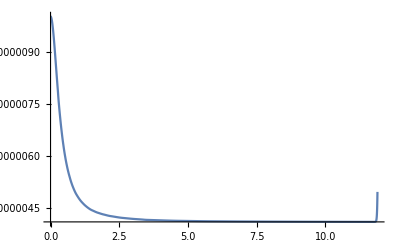

```mathematica
Plot[Evaluate[v[x]/.s],{x,0,11.9},PlotRange->All]
```